```mathematica
SetDirectory[NotebookDirectory[]<>"calcs"];
(*загружаем данные*)
evoAx1=Import["evoAx1.mx"];
evoBx1=Import["evoBx1.mx"];
evoAx2=Import["evoAx2.mx"];
evoBx2=Import["evoBx2.mx"];
evoAx3=Import["evoAx3.mx"];
evoBx3=Import["evoBx3.mx"];

evoAx1x8=Import["evoAx1x8.mx"];
evoBx1x8=Import["evoBx1x8.mx"];

evoAy1=Import["evoAy1.mx"];
evoBy1=Import["evoBy1.mx"];
evoAy2=Import["evoAy2.mx"];
evoBy2=Import["evoBy2.mx"];
evoAy3=Import["evoAy3.mx"];
evoBy3=Import["evoBy3.mx"];

pointsB2=Import["pointsB2.mx"];
pointsBd2=Import["pointsBd2.mx"];
pointsH2=Import["pointsH2.mx"];
pointsHd2=Import["pointsHd2.mx"];
pointsRB2=Import["pointsRB2.mx"];
pointsRBd2=Import["pointsRBd2.mx"];
pointsRH2=Import["pointsRH2.mx"];
pointsRHd2=Import["pointsRHd2.mx"];
pointsRB3=Import["pointsRB3.mx"];
pointsRH3=Import["pointsRH3.mx"];

pointsAm1=Import["pointsAm1.mx"];
pointsBm1=Import["pointsBm1.mx"];

evoAmBes1=Import["evoAmBes1.mx"];
evoAmHan1=Import["evoAmHan1.mx"];
evoBmBes1=Import["evoBmBes1.mx"];
evoBmHan1=Import["evoBmHan1.mx"];

evoAmBes1m15=Import["evoAmBes1m15.mx"];
evoAmHan1m15=Import["evoAmHan1m15.mx"];
evoBmBes1m15=Import["evoBmBes1m15.mx"];
evoBmHan1m15=Import["evoBmHan1m15.mx"];

evoAmBes2=Import["evoAmBes2.mx"];
evoAmHan2=Import["evoAmHan2.mx"];
evoBmBes2=Import["evoBmBes2.mx"];
evoBmHan2=Import["evoBmHan2.mx"];

evoAmAssymp1=Import["evoAmAssympEq.mx"];
evoBmAssymp1=Import["evoBmAssympEq.mx"];
evoAmAssymp2Old=Import["evoAmAssymp2.mx"];

evoAmBesAssymp2=Import["evoAmBesAssymp2.mx"];
evoAmHanAssymp2=Import["evoAmHanAssymp2.mx"];

evoAxUlt2=Import["evoAxUlt2.mx"];
```

```mathematica
evoAxUlt2
```

evoAxUlt2

```mathematica
(*в декартовы*)
evoAx1c=ToCartesian[evoAx1];
evoBx1c=ToCartesian[evoBx1];
evoAx2c=ToCartesian[evoAx2];
evoBx2c=ToCartesian[evoBx2];
evoAx3c=ToCartesian[evoAx3];
evoBx3c=ToCartesian[evoBx3];

evoAx1x8c=ToCartesian[evoAx1x8];
evoAx1x8c=ToCartesian[evoAx1x8];

evoAy1c=ToCartesian[evoAy1];
evoBy1c=ToCartesian[evoBy1];
evoAy2c=ToCartesian[evoAy2];
evoBy2c=ToCartesian[evoBy2];
evoAy3c=ToCartesian[evoAy3];
evoBy3c=ToCartesian[evoBy3];

pointsB2c=ToCartesianOld[pointsB2];
pointsBd2c=ToCartesianOld[pointsBd2];
pointsH2c=ToCartesianOld[pointsH2];
pointsHd2c=ToCartesianOld[pointsHd2];
pointsRB2c=ToCartesianOld[pointsRB2];
pointsRBd2c=ToCartesianOld[pointsRBd2];
pointsRH2c=ToCartesianOld[pointsRH2];
pointsRHd2c=ToCartesianOld[pointsRHd2];
pointsRB3c=ToCartesianOld[pointsRB3];
pointsRH3c=ToCartesianOld[pointsRH3];

evoAmBes1c=ToCartesian[evoAmBes1];
evoAmHan1c=ToCartesian[evoAmHan1];
evoBmBes1c=ToCartesian[evoBmBes1];
evoBmHan1c=ToCartesian[evoBmHan1];
evoAm1=Join[evoAmBes1,evoAmHan1,1];
evoBm1=Join[evoBmBes1,evoBmHan1,1];
evoAm1c=ToCartesian[evoAm1];
evoBm1c=ToCartesian[evoBm1];

evoAmBes1m15c=ToCartesian[evoAmBes1m15];
evoAmHan1m15c=ToCartesian[evoAmHan1m15];
evoBmBes1m15c=ToCartesian[evoBmBes1m15];
evoBmHan1m15c=ToCartesian[evoBmHan1m15];
evoAm1m15=Join[evoAmBes1m15,evoAmHan1m15,1];
evoBm1m15=Join[evoBmBes1m15,evoBmHan1m15,1];
evoAm1m15c=ToCartesian[evoAm1m15];
evoBm1m15c=ToCartesian[evoBm1m15];

evoAmBes2c=ToCartesian[evoAmBes2];
evoAmHan2c=ToCartesian[evoAmHan2];
evoBmBes2c=ToCartesian[evoBmBes2];
evoBmHan2c=ToCartesian[evoBmHan2];
evoAm2=Join[evoAmBes2,evoAmHan2,1];
evoBm2=Join[evoBmBes2,evoBmHan2,1];
evoAm2c=ToCartesian[evoAm2];
evoBm2c=ToCartesian[evoBm2];

evoAmAssymp1c=ToCartesian[evoAmAssymp1];
evoBmAssymp1c=ToCartesian[evoBmAssymp1];
evoAmAssymp2Oldc=ToCartesian[evoAmAssymp2Old];

evoAmBesAssymp2c=ToCartesian[evoAmBesAssymp2];
evoAmHanAssymp2c=ToCartesian[evoAmHanAssymp2];
```

```mathematica
(*загрузить функциия из Get zeros functions.nb*)
(*нужные уравнения*)
jb[n_,x_]:=SphericalBesselJ[n,x]
yb[n_,x_]:=SphericalBesselY[n,x]
h1[n_,x_]:=SphericalHankelH1[n,x]
h1d[k_,x_]:=h1[k-1,x]-(k+1)/x h1[k,x]
jbd[k_,x_]:=-jb[k,x]/(2 x)+1/2 (jb[-1+k,x]-jb[1+k,x])
ψ[n_,x_]:=x jb[n,x];
ξ[n_,x_]:=x h1[n,x];
ψd[k_,x_]:=jb[k,x]+x (-jb[k,x]/(2 x)+1/2 (jb[-1+k,x]-jb[1+k,x]))
ξd[k_,x_]:=h1[k,x]+x (-h1[k,x]/(2 x)+1/2 (h1[-1+k,x]-h1[1+k,x]))
ψd2[n_,x_]:=(√(π/2) (n+n^2-x^2) BesselJ[1/2+n,x])/x^(3/2)
ξd2[k_,x_]:=((k+k^2-x^2) SphericalHankelH1[k,x])/x
A1[n_,x_,y_]:=y ψ[n,y ]ξd[n,x]-x ξ[n,x]ψd[n,y]
B1[n_,x_,y_]:=x ψ[n,y ]ξd[n,x]-y ξ[n,x]ψd[n,y]
g[n_,x_]:=ψd[n,x]/ψ[n,x]
f[n_,x_]:=ξd[n,x]/ξ[n,x]
gd[n_,x_]:=ψd2[n,x]/ψ[n,x]-ψd[n,x]^2/ψ[n,x]^2
fd[n_,x_]:=ξd2[n,x]/ψ[n,x]-ξd[n,x]^2/ψ[n,x]^2

A1a[n_,x_,dm_]:=1+I x^2 jb[n,x]h1[n,x](x gd[n,x] -g[n,x])dm
B1a[n_,x_,dm_]:=1+I x^2 jb[n,x]h1[n,x](x gd[n,x] +g[n,x])dm
A1a2[n_,x_,dm_]:=x(I √((n+1)/n)  ψ[n,I √((n+1)/n) x ]+dm( ψ[n,I √((n+1)/n) x ]+I √((n+1)/n)))ξd[n,x]-x ξ[n,x]ψd[n, m x]
a[n_,x_,y_]:=(y ψ[n,y ]ψd[n,x]-x ψ[n,x]ψd[n,y])/A1[n,x,y]
b[n_,x_,y_]:=(x ψ[n,y ]ψd[n,x]-y ψ[n,x]ψd[n,y])/B1[n,x,y]
aiZ=−2.3381074105; (*dlmf §9.9(v) for 1 order*)
aiDZ=−1.0187929716;
HankelZero[v_]:=v-2^(-1/3)Exp[-I 2π/3]aiZ v^(1/3)(*+(3/10)2^(-2/3)Exp[-I 4π/3] aiZ^2/v^(1/3)*)(* Andrés Cruz 1982*)
HankelDZero[v_]:=v-2^(-1/3)Exp[-I 2π/3]aiDZ v^(1/3)(*+2^(-2/3)Exp[-I 4π/3](3aiDZ^2/10 +aiDZ/5)/v^(1/3)*)(* Andrés Cruz 1982*)
```

```mathematica
(*находим корни для всех рассматриваемых случаев*)
(*x фиксированнный*)
{n=10, amax=42};
argxStart=0.0;
xc:=x Exp[I argx];
yc:=y Exp[I argy];
n2=100;
```

```mathematica
x=10; argx=argxStart;
pointsAx1=GetZeros[A1[n,xc,yc],{argy,y},{{-π/2,π/2},{0.1,amax}},10];
pointsBx1=GetZeros[B1[n,xc,yc],{argy,y},{{-π/2,π/2},{0.1,amax}},10]; Clear[argx];
evoAx1=MultipleEvolution[A1[n,xc,yc],{argy,y},pointsAx1,{argx,argxStart,#,0.001}]&/@{-π/2,π/2};
evoBx1=MultipleEvolution[B1[n,xc,yc],{argy,y},pointsBx1,{argx,argxStart,#,0.001}]&/@{-π/2,π/2};
evoAx1=evoMerge[evoAx1];
evoBx1=evoMerge[evoBx1];
```

```mathematica
x=20;argx=argxStart;amax=8x; nump=Floor[amax/2];
pointsAx2=GetZeros[A1[n,xc,yc],{argy,y},{{0},{n-2,amax+2}},nump];
pointsBx2=GetZeros[B1[n,xc,yc],{argy,y},{{0},{n-2,amax+2}},nump];Clear[argx];
evoAx2=MultipleEvolution[A1[n,xc,yc],{argy,y},pointsAx2,{argx,argxStart,#,0.01}]&/@{-π/2,π/2};
evoBx2=MultipleEvolution[B1[n,xc,yc],{argy,y},pointsBx2,{argx,argxStart,#,0.01}]&/@{-π/2,π/2};
evoAx2=evoMerge[evoAx2];
evoBx2=evoMerge[evoBx2];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

```mathematica
(*сохранить*)
Export["evoAx2.mx",evoAx2];
Export["evoBx2.mx",evoBx2];
```

```mathematica
x=5;argx=argxStart;amax=80;
pointsAx3=GetZeros[A1[n,xc,yc],{argy,y},{{0},{0.1,amax}},80];
pointsBx3=GetZeros[B1[n,xc,yc],{argy,y},{{0},{0.1,amax}},80];Clear[argx];
evoAx3=MultipleEvolution[A1[n,xc,yc],{argy,y},pointsAx3,{argx,argxStart,#,0.01}]&/@{-π/2,π/2};
evoBx3=MultipleEvolution[B1[n,xc,yc],{argy,y},pointsBx3,{argx,argxStart,#,0.01}]&/@{-π/2,π/2};
evoAx3=evoMerge[evoAx3];
evoBx3=evoMerge[evoBx3];
(*ищем асимптотический корени x<<n*) 
{x=5};argxStart=0;argx= argxStart;
pointsAx3a=Flatten[GetZeros[A1[n,xc,yc],{argy,y},{{#},{x-2,x+2}},5]&/@{-π/2,π/2},1]; Clear[argx];
evoAx3a=MultipleEvolution[A1[n,xc,yc],{argy,y},pointsAx3a,{argx, argxStart,#,0.01},"List"]&/@{-π/2,π/2};
evoAx3a=evoMerge[evoAx3a];
(*добавляем к остальным*)
evoAx3=Join[evoAx3,evoAx3a];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

```mathematica
(*сохранить*)
Export["evoAx3.mx",evoAx3];
Export["evoBx3.mx",evoBx3];
```

```mathematica
(*ищем асимптотический корени x<<n*) 
{x=5};argxStart=0;argx= argxStart;
pointsAx3a=Flatten[GetZeros[A1[n,xc,yc],{argy,y},{{#},{x-2,x+2}},5]&/@{-π/2,π/2},1]; Clear[argx];
evoAx3a=MultipleEvolution[A1[n,xc,yc],{argy,y},pointsAx3a,{argx, argxStart,#,0.01}]&/@{-π/2,π/2};
test=evoAx3a;
evoAx3a=evoMerge[evoAx3a];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

```mathematica
Clear[n,x,y, amax, argx,argy]
```

```mathematica
{n=10, amax=20};
 argyStart=0.0;
```

```mathematica
y=10;argy= argyStart;
pointsAy1=GetZeros[A1[n,xc,yc],{argx,x},{{-π/2,π/2},{0.1,amax}},10];
pointsBy1=GetZeros[B1[n,xc,yc],{argx,x},{{-π/2,π/2},{0.1,amax}},10];Clear[argy];
evoAy1=MultipleEvolution[A1[n,xc,yc],{argx,x},pointsAy1,{argy,argyStart,#,0.001},"List"]&/@{-π/2,π/2};
evoBy1=MultipleEvolution[B1[n,xc,yc],{argx,x},pointsBy1,{argy,argyStart,#,0.001},"List"]&/@{-π/2,π/2};
evoAy1=evoMerge[evoAy1];
evoBy1=evoMerge[evoBy1];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
{y=20};argy= 0;
pointsAy2=GetZeros[A1[n,xc,yc],{argx,x},{{-π/2-0.1,π/2},{0.1,amax}},10]; 
pointsBy2=GetZeros[B1[n,xc,yc],{argx,x},{{-π/2-0.1,π/2},{0.1,amax}},10];Clear[argy];
evoAy2=MultipleEvolution[A1[n,xc,yc],{argx,x},pointsAy2,{argy,argyStart,#,0.01},"List"]&/@{-π/2,π/2};
evoBy2=MultipleEvolution[B1[n,xc,yc],{argx,x},pointsBy2,{argy,argyStart,#,0.01},"List"]&/@{-π/2,π/2};
evoAy2=evoMerge[evoAy2];
evoBy2=evoMerge[evoBy2];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
{y=5};argy= argyStart;
pointsAy3=GetZeros[A1[n,xc,yc],{argx,x},{{-π/2,π/2},{0.1,amax}},10];
pointsBy3=GetZeros[B1[n,xc,yc],{argx,x},{{-π/2,π/2},{0.1,amax}},10];Clear[argy];
evoAy3=MultipleEvolution[A1[n,xc,yc],{argx,x},pointsAy3,{argy,argyStart,#,0.01},"List"]&/@{-π/2,π/2};
evoBy3=MultipleEvolution[B1[n,xc,yc],{argx,x},pointsBy3,{argy,argyStart,#,0.01},"List"]&/@{-π/2,π/2};
evoAy3=evoMerge[evoAy3];
evoBy3=evoMerge[evoBy3];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*ищем асимптотический корени у>>n*) 
{y=20};amax=20;argyStart=-0.1;argy=argyStart;
pointsAy2a=GetZeros[A1[n,xc,yc],{argx,x},{{-π/2,π/2},{y-1,y+1}},2];
pointsBy2a=GetZeros[B1[n,xc,yc],{argx,x},{{-π/2,π/2},{y-1,y+1}},5]; Clear[argy];
evoAy2a=MultipleEvolution[A1[n,xc,yc],{argx,x},pointsAy2a,{argy, argyStart,#,0.001},"List"]&/@{-π/2,π/2};
evoBy2a=MultipleEvolution[B1[n,xc,yc],{argx,x},pointsBy2a,{argy, argyStart,#,0.001},"List"]&/@{-π/2,π/2};
evoAy2a=evoMerge[evoAy2a];
evoBy2a=evoMerge[evoBy2a];
evoAy2a=Downsample[evoAy2a,{1,10,1}]; (*этот корень расчитать с меньшим шагом*)
evoBy2a=Downsample[evoBy2a,{1,10,1}];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
(*ищем асимптотический корени у<<n*) 
{y=5};argyStart=-0.1;argy= argyStart;
pointsAy3a=GetZeros[A1[n,xc,yc],{argx,x},{{1,π/2},{y-1,y+1}},2]; Clear[argy];
evoAy3a=MultipleEvolution[A1[n,xc,yc],{argx,x},pointsAy3a,{argy, argyStart,#,0.01},"List"]&/@{-π/2,π/2};
evoAy3a=evoMerge[evoAy3a];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

```mathematica
Clear[x,y, amax, argx,argy]
```

```mathematica
(*объединяем с остальными корнями*)
evoAy2=Join[evoAy2,evoAy2a];
evoBy2=Join[evoBy2,evoBy2a];
evoAy3=Join[evoAy3,evoAy3a];
evoAx3=Join[evoAx3,evoAx3a];
```

```mathematica
(*корни бесселя и ганкеля*)
Clear[x]
pointsB2=GetZeros[ψ[n,x Exp[I argx]],{argx,x},{{-π/8,π/8},{0.1,4n+5}},10];
pointsBd2=GetZeros[jbd[n,x Exp[I argx]],{argx,x},{{-π/8,π/8},{0.1,4n+5}},10];
pointsH2=GetZeros[ξ[n,x Exp[I argx]],{argx,x},{{-π,0},{5,1.5n}},20];
pointsHd2=GetZeros[h1d[n,x Exp[I argx]],{argx,x},{{-π,0},{5,1.5n}},20];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

```mathematica
Clear[x]
pointsRB2=GetZeros[ψ[n,x Exp[I argx]],{argx,x},{{-π/8,π/8},{0.1,4n+5}},10];
pointsRBd2=GetZeros[ψd[n,x Exp[I argx]],{argx,x},{{-π/8,π/8},{0.1,4n+5}},10];
pointsRH2=GetZeros[ξ[n,x Exp[I argx]],{argx,x},{{-π,1},{5,1.5n}},20];
pointsRHd2=GetZeros[ξd[n,x Exp[I argx]],{argx,x},{{-π,1},{5,1.5n}},20];
```

```mathematica
pointsRB3=GetZeros[ψ[n-1,x Exp[I argx]],{argx,x},{{0},{0.1,4n+5}},20];
pointsRH3=GetZeros[ξ[n+1,x Exp[I argx]],{argx,x},{{-π,1},{5,1.5n}},20];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
SetDirectory[NotebookDirectory[]<>"calcs"];
Export["pointsRB3.mx",pointsRB3];
Export["pointsRH3.mx",pointsRH3];
```

```mathematica
(*сохранить*)
Export["pointsRB2.mx",pointsRB2];
Export["pointsRBd2.mx",pointsRBd2];
Export["pointsRH2.mx",pointsRH2];
Export["pointsRHd2.mx",pointsRHd2];
```

```mathematica
(*x m coordinates*)
n=10;m=2; argm=-1;argStart=argm;
pointsAmBes1=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-argm},{n/m/2,4n/m}},30];
pointsAmHan1=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-1.6,0.5},{n}},20];
pointsBmBes1=GetZeros[B1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-argm},{n/m/2,4n/m}},30];
pointsBmHan1=GetZeros[B1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-1.6,0.5},{n}},20];
pointsAmHan1=GatePoints[pointsAmHan1,{{-1.6,0.5},{n/2,2n}}];
pointsBmHan1=GatePoints[pointsBmHan1,{{-1.6,0.5},{n/2,2n}}];
Clear[argm];
evoAmBes1=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsAmBes1,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoAmHan1=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsAmHan1,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoBmBes1=MultipleEvolution[B1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsBmBes1,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoBmHan1=MultipleEvolution[B1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsBmHan1,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoAmBes1=evoMerge[evoAmBes1];
evoAmHan1=evoMerge[evoAmHan1];
evoBmBes1=evoMerge[evoBmBes1];
evoBmHan1=evoMerge[evoBmHan1];
evoAm1=Join[evoAmBes1,evoAmHan1,1];
evoBm1=Join[evoBmBes1,evoBmHan1,1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
evoAmBes1c=ToCartesian[evoAmBes1];
evoAmHan1c=ToCartesian[evoAmHan1];
evoBmBes1c=ToCartesian[evoBmBes1];
evoBmHan1c=ToCartesian[evoBmHan1];
evoAm1c=ToCartesian[evoAm1];
evoBm1c=ToCartesian[evoBm1];
```

```mathematica
(*сохранить*)
Export["evoAmBes1.mx",evoAmBes1];
Export["evoAmHan1.mx",evoAmHan1];
Export["evoBmBes1.mx",evoBmBes1];
Export["evoBmHan1.mx",evoBmHan1];
```

```mathematica
n=10;m=1.1; argm=-1;argStart=argm;
pointsAmBes2=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-argm},{n/m/2,4n/m}},30];
pointsAmHan2=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-1.6,0.5},{n}},20];
pointsBmBes2=GetZeros[B1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-argm},{n/m/2,4n/m}},30];
pointsBmHan2=GetZeros[B1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-1.6,0.5},{n}},20];
pointsAmHan2=GatePoints[pointsAmHan2,{{-1.6,0.5},{n/2,2n}}];
pointsBmHan2=GatePoints[pointsBmHan2,{{-1.6,0.5},{n/2,2n}}];
Clear[argm];
evoAmBes2=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsAmBes2,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoAmHan2=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsAmHan2,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoBmBes2=MultipleEvolution[B1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsBmBes2,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoBmHan2=MultipleEvolution[B1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsBmHan2,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoAmBes2=evoMerge[evoAmBes2];
evoAmHan2=evoMerge[evoAmHan2];
evoBmBes2=evoMerge[evoBmBes2];
evoBmHan2=evoMerge[evoBmHan2];
evoAm2=Join[evoAmBes2,evoAmHan2,1];
evoBm2=Join[evoBmBes2,evoBmHan2,1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
(*сохранить*)
Export["evoAmBes2.mx",evoAmBes2];
Export["evoAmHan2.mx",evoAmHan2];
Export["evoBmBes2.mx",evoBmBes2];
Export["evoBmHan2.mx",evoBmHan2];
```

```mathematica
n=10;m=1.01; argm=-1;argStart=argm;
pointsAmBes3=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-argm},{n/m/2,4n/m}},30];
pointsAmHan3=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-1.6,0.5},{n}},20];
pointsBmBes3=GetZeros[B1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-argm},{n/m/2,4n/m}},30];
pointsBmHan3=GetZeros[B1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-1.6,0.5},{n}},20];
pointsAmHan3=GatePoints[pointsAmHan3,{{-1.6,0.5},{n/2,2n}}];
pointsBmHan3=GatePoints[pointsBmHan3,{{-1.6,0.5},{n/2,2n}}];
Clear[argm];
evoAmBes3=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsAmBes3,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoAmHan3=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsAmHan3,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoBmBes3=MultipleEvolution[B1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsBmBes3,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoBmHan3=MultipleEvolution[B1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsBmHan3,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoAmBes3=evoMerge[evoAmBes3];
evoAmHan3=evoMerge[evoAmHan3];
evoBmBes3=evoMerge[evoBmBes3];
evoBmHan3=evoMerge[evoBmHan3];
evoAm3=Join[evoAmBes3,evoAmHan3,1];
evoBm3=Join[evoBmBes3,evoBmHan3,1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

```mathematica
(*рассмотрим переход асимптотики по модулю*)
n1=10;m=1.01; argm=0.0;Start=m;mp=0;
pointsAmAssymp1=GetZeros[A1[n1,x Exp[I argx],x Exp[I argx](1+0.01*10^-mp)  ],{argx,x},{{-π/2,π/8},{n1/2,2n1}},10];
pointsBmAssymp1=Join[GetZeros[B1[n1,x Exp[I argx],x Exp[I argx](1+0.01*10^-mp)  ],{argx,x},{{-π/2,π/8},{n1/2,2n1}},10],GetZeros[B1[n1,x Exp[I argx],x Exp[I argx](1+0.01*10^0)  ],{argx,x},{{-1.47},{8,9}},3]];(*костыль для 1 точки*)
Clear[m,mp];
evoAmAssymp1=MultipleEvolution[A1a[n1,x Exp[I argx],0.01*10^(- mp) ],{argx,x},pointsAmAssymp1,{mp,0,30,0.1}];
evoBmAssymp1=MultipleEvolution[B1a[n1,x Exp[I argx],0.01*10^(- mp) ],{argx,x},pointsBmAssymp1,{mp,0,30,0.1}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
evoAmAssymp1c=ToCartesian[evoAmAssymp1];
evoBmAssymp1c=ToCartesian[evoBmAssymp1];
```

```mathematica
Export["evoAmAssympEq.mx",evoAmAssymp1];
Export["evoBmAssympEq.mx",evoBmAssymp1];
```

```mathematica
evoAmAssympF=Import["evoAmAssymp2.mx"];
```

```mathematica
n=10;m=2; argm=0;argStart=argm;
pointsAmAssymp12=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-π/2-0.1,π/8},{5,20}},30];
pointsBmAssymp12=GetZeros[B1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-π/2-0.1,π/8},{5,20}},30];
Clear[m,mp];
evoAmAssymp12=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx](1+10^mp) Exp[I argm]],{argx,x},pointsAmAssymp12,{mp,0,-2,0.01}];
evoBmAssymp12=MultipleEvolution[B1[n,x Exp[I argx],x Exp[I argx](1+10^mp) Exp[I argm]],{argx,x},pointsBmAssymp12,{mp,0,-2,0.01}];
evoAmAssymp12c=ToCartesian[evoAmAssymp12];
evoBmAssymp12c=ToCartesian[evoBmAssymp12];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

```mathematica
Export["evoAmAssymp12.mx",evoAmAssymp12];
Export["evoBmAssymp12.mx",evoBmAssymp12];
```

```mathematica
(*рассмотрим переход асимптотики по модулю m=I*)
n1=10;m=1.01; argm=0.0;Start=m;mp=0;
pointsAmAssymp2=GetZeros[A1[n1,x Exp[I argx],x Exp[I argx] √((n1+1)/n1) Exp[I argm] ],{argx,x},{{-π/2-0.2,0},{3,20}},10];
Clear[m,mp,argm];
evoAmAssymp2=MultipleEvolution[A1[n1,x Exp[I argx],x Exp[I argx] √((n1+1)/n1)Exp[I argm] ],{argx,x},pointsAmAssymp2,{argm,0,#,0.01}]&/@{-π/2,π/2};
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
evoAmAssymp2Oldc=ToCartesian[evoAmAssymp2Old];
```

```mathematica
evoAmAssymp22=MultipleEvolution[A1[n1,x Exp[I argx],x Exp[I argx] √((n1+1)/n1)(1+0.3mp) I],{argx,x},pointsAmAssympI16,{mp,1,-1,0.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

```mathematica
pointsAmAssymp3=GetZeros[A1[n1,x Exp[I argx],x Exp[I argx] √((n1+1)/n1)I  ],{argx,x},{{-π/2-0.2,0},{0.1,20}},100];
```

FindRoot::jsing: Encountered a singular Jacobian at the point {argx,x} = {-1.76834,3.65595×10^-6}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {argx,x} = {-1.77255,0.000133679}. Try perturbing the initial point(s).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {argx,x} = {-1.69647,0.0000425933}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

```mathematica
Export["pointsAmAssympI16.mx",pointsAmAssympI16];
```

```mathematica
evoAmAssymp2Old=Import["evoAmAssymp2.mx"];
```

```mathematica
√((n1+1)/n1)//N
```

1.04881

```mathematica
(*рассмотрим переход асимптотики по модулю m=I*)
n=10;m=√((n+1)/n); argm=-1;argStart=argm;
pointsAmBesAssymp2=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-argm},{n/m/2,4n/m}},30];
pointsAmHanAssymp2=GetZeros[A1[n,x Exp[I argx],x Exp[I argx](m Exp[I argm]) ],{argx,x},{{-1.6,0.5},{n}},20];
pointsAmHanAssymp2=GatePoints[pointsAmHanAssymp2,{{-1.6,0.5},{n/2,2n}}];
Clear[argm];
evoAmBesAssymp2=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsAmBesAssymp2,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoAmHanAssymp2=MultipleEvolution[A1[n,x Exp[I argx],x Exp[I argx]m Exp[I argm]],{argx,x},pointsAmHanAssymp2,{argm,argStart,#,0.01}]&/@{-π/2,π/2};
evoAmBesAssymp2=evoMerge[evoAmBesAssymp2];
evoAmHanAssymp2=evoMerge[evoAmHanAssymp2];
evoAmAssymp2=Join[evoAmBesAssymp2,evoAmHanAssymp2,1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
evoAmBesAssymp2c=ToCartesian[evoAmBesAssymp2];
evoAmHanAssymp2c=ToCartesian[evoAmHanAssymp2];
evoAmAssymp2c=ToCartesian[evoAmAssymp2];
```

```mathematica
(*сохранить*)
Export["evoAmBesAssymp2.mx",evoAmBesAssymp2];
Export["evoAmHanAssymp2.mx",evoAmHanAssymp2];
```

```mathematica
n2=100;m=1.6; imm=0;argStart=imm;
pointsAm2=GetZeros[A1[n2,x Exp[I argx],x Exp[I argx](m+I imm) ],{argx,x},{{0},{n2/2,1.5n2}},100];Clear[imm];
evoAm2=MultipleEvolution[A1[n2,x Exp[I argx],x Exp[I argx](m+I imm)],{argx,x},pointsAm2,{imm,argStart,1,0.01},"List"];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

```mathematica
evoAm2c=ToCartesian[evoAm2];
```

```mathematica
n1=20;m=1.6; imm=0;argStart=imm;
pointsAm3=GetZerosHankel[A1[in,x Exp[I argx],x Exp[I argx](m+I ) ],{argx,x},{in,10,200}];
pointsAm3c=ToCartesianOld[pointsAm3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

$Aborted

```mathematica
pointsHd=GetZerosHankel[h1d[in,x Exp[I argx] ],{argx,x},{in,10,200}];
pointsHdc=ToCartesianOld[pointsHd];
pointsH=GetZerosHankel[h1[in,x Exp[I argx] ],{argx,x},{in,10,200}];
pointsHc=ToCartesianOld[pointsH];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pointsAproxHankelD=Table[HankelDZero[v+1/2],{v,10,200,1}];(*spherical*)
pointsAproxHankelDc=Map[{Re[#],Im[#]}&,pointsAproxHankelD];
pointsAproxHankelDp=Map[{Arg[#],Abs[#]}&,pointsAproxHankelD];
pointsAproxHankel=Table[HankelZero[v+1/2],{v,10,200,1}];(*spherical*)
pointsAproxHankelc=Map[{Re[#],Im[#]}&,pointsAproxHankel];
pointsAproxHankelp=Map[{Arg[#],Abs[#]}&,pointsAproxHankel];
```

```mathematica
pointsHd=GetNearHankelZeros[h1d[in,x Exp[I argx] ],{argx,x},pointsAproxHankelDp,{in,10,200,1}];
pointsHdc=ToCartesianOld[pointsHd];
pointsH=GetNearHankelZeros[h1[in,x Exp[I argx] ],{argx,x},pointsAproxHankelp,{in,10,200,1}];
pointsHc=ToCartesianOld[pointsH];
```

```mathematica
m=1.6; argm=π/5;imm=1;
pointsAm3=GetNearHankelZeros[A1[in,x Exp[I argx],x Exp[I argx](m +I imm) ],{argx,x},pointsAproxHankelDp,{in, 10,200,1}]; Clear[m,argm,imm];
pointsAm3c=ToCartesianOld[pointsAm3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Arg[3+I]
```

0.558599

```mathematica
(*сохроняем в файлы*)
SetDirectory[NotebookDirectory[]<>"calcs"];

Export["evoAx1.mx",evoAx1];
Export["evoBx1.mx",evoBx1];
Export["evoAx2.mx",evoAx2];
Export["evoBx2.mx",evoBx2];
Export["evoAx3.mx",evoAx3];
Export["evoBx3.mx",evoBx3];

Export["evoAy1.mx",evoAy1];
Export["evoBy1.mx",evoBy1];
Export["evoAy2.mx",evoAy2];
Export["evoBy2.mx",evoBy2];
Export["evoAy3.mx",evoAy3];
Export["evoBy3.mx",evoBy3];

Export["pointsB2.mx",pointsB2];
Export["pointsBd2.mx",pointsBd2];
Export["pointsH2.mx",pointsH2];
Export["pointsHd2.mx",pointsHd2];

Export["pointsAm1.mx",pointsAm1];
Export["pointsBm1.mx",pointsBm1];
Export["evoAm1.mx",evoAm1];
Export["evoBm1.mx",evoBm1];

Export["evoAm2.mx",evoAm2];
```

```mathematica
evoAx2//Dimensions
```

{47,315,3}

```mathematica
(*записываем в файлы*)
SetDirectory[NotebookDirectory[]<>"figures"];
MergeArrays[lists_]:=Module[{size,sizes,out},
size=lists//Length;
sizes=Length/@lists;
out=PadRight[lists,{size,Max[sizes],2},"NaN"]//N;
Join@@Append[out,2]
]
```

```mathematica
PrepareArray1[list_]:=Module[{rt,mv,pr},
{rt,mv,pr}=list//Dimensions;
ArrayReshape[list,{rt*mv,pr}]//N]

Export["fig1a.txt",MergeArrays[{
PrepareArray1[evoAx2]⟦;;,{3,1}⟧,
PrepareArray1[evoAx3]⟦;;,{3,1}⟧,
PrepareArray1[evoAy2]⟦;;,{1,3}⟧,
PrepareArray1[evoAy3]⟦;;,{1,3}⟧}],"Table"];

Export["fig1b.txt",MergeArrays[{
PrepareArray1[evoBx2]⟦;;,{3,1}⟧,
PrepareArray1[evoBx3]⟦;;,{3,1}⟧,
PrepareArray1[evoBy2]⟦;;,{1,3}⟧,
PrepareArray1[evoBy3]⟦;;,{1,3}⟧}],"Table"];

Export["fig2.txt",MergeArrays[{
Join[PrepareArray1[evoAx2]⟦;;,{3,1}⟧,PrepareArray1[evoBx2]⟦;;,{3,1}⟧],
Join[PrepareArray1[evoAx3]⟦;;,{3,1}⟧,PrepareArray1[evoBx3]⟦;;,{3,1}⟧],
Join[PrepareArray1[evoAy2]⟦;;,{1,3}⟧,PrepareArray1[evoBy2]⟦;;,{1,3}⟧],
Join[PrepareArray1[evoAy3]⟦;;,{1,3}⟧,PrepareArray1[evoBy3]⟦;;,{1,3}⟧]}],"Table"];

Export["fig2b.txt",MergeArrays[{
PrepareArray1[evoAx3]⟦;;,{3,1}⟧,
PrepareArray1[evoBx3]⟦;;,{3,1}⟧}],"Table"];

Export["fig3.txt",MergeArrays[{
PrepareArray1[evoAx2]⟦;;,{3,1}⟧,
PrepareArray1[evoAx3]⟦;;,{3,1}⟧,
PrepareArray1[evoAx1]⟦;;,{3,1}⟧}],"Table"];
```

```mathematica
(*сохраняем траектории*)
SetDirectory[NotebookDirectory[]<>"figures"];
PrepareArray2[list_]:=Module[{rt,mv,pr},
{rt,mv,pr}=list//Dimensions;
Join@@Append[list,2]//N]

Export["fig4_1.txt",PrepareArray2[evoAx2c⟦1;;9⟧],"Table"];
Export["fig4_2.txt",PrepareArray2[evoBx2c⟦1;;9⟧],"Table"];
Export["fig4_1arrows.txt",ArrayReshape[GetArrowsArray[evoAx2c,157]⟦1;;9⟧,{9,4}],"Table"];
Export["fig4_2arrows.txt",ArrayReshape[GetArrowsArray[evoBx2c,157]⟦1;;9⟧,{9,4}],"Table"];

Export["fig5_1.txt",PrepareArray2[evoAx3c⟦1;;9⟧],"Table"];
Export["fig5_2.txt",PrepareArray2[evoBx3c⟦1;;9⟧],"Table"];
Export["fig5_1arrows.txt",ArrayReshape[GetArrowsArray[evoAx3c,157]⟦1;;9⟧,{9,4}],"Table"];
Export["fig5_2arrows.txt",ArrayReshape[GetArrowsArray[evoBx3c,157]⟦1;;9⟧,{9,4}],"Table"];

evoAx1cD=Downsample[evoAx1c,{1,10,1}];
evoBx1cD=Downsample[evoBx1c,{1,10,1}];
Export["fig6_1.txt",PrepareArray2[evoAx1cD],"Table"];
Export["fig6_2.txt",PrepareArray2[evoBx1cD],"Table"];
Export["fig6_1arrows.txt",ArrayReshape[GetArrowsArray[evoAx1cD,157],{9,4}],"Table"];
Export["fig6_2arrows.txt",ArrayReshape[GetArrowsArray[evoBx1cD,157],{8,4}],"Table"];


Export["fig7_1.txt",PrepareArray2[evoAy2c],"Table"];
Export["fig7_2.txt",PrepareArray2[evoBy2c],"Table"];
Export["fig7_1arrows.txt",ArrayReshape[GetArrowsArray[evoAy2c,157],{9,4}],"Table"];
Export["fig7_2arrows.txt",ArrayReshape[GetArrowsArray[evoBy2c,157],{9,4}],"Table"];

Export["fig8_1.txt",PrepareArray2[evoAy3c],"Table"];
Export["fig8_2.txt",PrepareArray2[evoBy3c],"Table"];
Export["fig8_1arrows.txt",ArrayReshape[GetArrowsArray[evoAy3c,157],{9,4}],"Table"];
Export["fig8_2arrows.txt",ArrayReshape[GetArrowsArray[evoBy3c,157],{9,4}],"Table"];

evoAy1cD=Downsample[evoAy1c,{1,10,1}];
evoBy1cD=Downsample[evoBy1c,{1,10,1}];
Export["fig9_1.txt",PrepareArray2[evoAy1cD],"Table"];
Export["fig9_2.txt",PrepareArray2[evoBy1cD],"Table"];
Export["fig9_1arrows.txt",ArrayReshape[GetArrowsArray[evoAy1cD,157],{9,4}],"Table"];
Export["fig9_2arrows.txt",ArrayReshape[GetArrowsArray[evoBy1cD,157],{9,4}],"Table"];

Export["fig10a_1.txt",PrepareArray2[evoAmBes1c],"Table"];
Export["fig10a_2.txt",PrepareArray2[evoAmHan1c],"Table"];
Export["fig10a_1arrows.txt",ArrayReshape[GetArrowsArray[evoAmBes1c,157],{9,4}],"Table"];
Export["fig10a_2arrows.txt",ArrayReshape[GetArrowsArray[evoAmHan1c,157],{9,4}],"Table"];

Export["fig10b_1.txt",PrepareArray2[evoBmBes1c],"Table"];
Export["fig10b_2.txt",PrepareArray2[evoBmHan1c],"Table"];
Export["fig10b_1arrows.txt",ArrayReshape[GetArrowsArray[evoBmBes1c,157],{9,4}],"Table"];
Export["fig10b_2arrows.txt",ArrayReshape[GetArrowsArray[evoBmHan1c,157],{9,4}],"Table"];

Export["fig11a_1.txt",PrepareArray2[evoAmBes2c],"Table"];
Export["fig11a_2.txt",PrepareArray2[evoAmHan2c],"Table"];
Export["fig11a_1arrows.txt",ArrayReshape[GetArrowsArray[evoAmBes2c,157],{9,4}],"Table"];
Export["fig11a_2arrows.txt",ArrayReshape[GetArrowsArray[evoAmHan2c,157],{9,4}],"Table"];

Export["fig11b_1.txt",PrepareArray2[evoBmBes2c],"Table"];
Export["fig11b_2.txt",PrepareArray2[evoBmHan2c],"Table"];
Export["fig11b_1arrows.txt",ArrayReshape[GetArrowsArray[evoBmBes2c,157],{9,4}],"Table"];
Export["fig11b_2arrows.txt",ArrayReshape[GetArrowsArray[evoBmHan2c,157],{9,4}],"Table"];

evoAmAssymp1cToWrite=evoAmAssymp1c;
evoAmAssymp1cToWrite⟦;;,;;,3⟧=-evoAmAssymp1c⟦;;,;;,3⟧-2//N;
evoBmAssymp1cToWrite=evoBmAssymp1c;
evoBmAssymp1cToWrite⟦;;,;;,3⟧=-evoBmAssymp1c⟦;;,;;,3⟧-2//N;

Export["fig12a_1.txt",PrepareArray2[evoAmAssymp1cToWrite],"Table"];
Export["fig12a_2.txt",PrepareArray2[evoBmAssymp1cToWrite],"Table"];
Export["fig12a_1arrows.txt",ArrayReshape[GetArrowsArray[evoAmAssymp1c,1],{9,4}],"Table"];
Export["fig12a_2arrows.txt",ArrayReshape[GetArrowsArray[evoBmAssymp1c,1],{9,4}],"Table"];

Export["fig12b_1.txt",PrepareArray2[evoAmBesAssymp2c],"Table"];
Export["fig12b_2.txt",PrepareArray2[evoAmHanAssymp2c],"Table"];
Export["fig12b_1arrows.txt",ArrayReshape[GetArrowsArray[evoAmBesAssymp2c,157],{9,4}],"Table"];
Export["fig12b_2arrows.txt",ArrayReshape[GetArrowsArray[evoAmHanAssymp2c,157],{9,4}],"Table"];
```

```mathematica
evoBmAssymp1cToWrite//Dimensions
```

{7,301,3}

```mathematica
Export["Bessel_zeros.txt",pointsRB2c,"Table"];
Export["Bessel_deriv_zeros.txt",pointsRBd2c,"Table"];
Export["Hankel_zeros.txt",pointsRH2c,"Table"];
Export["Hankel_deriv_zeros.txt",pointsRHd2c,"Table"];
Export["Bessel_np1_zeros.txt",pointsRB3c,"Table"];
Export["Hankel_np1_zeros.txt",pointsRH3c,"Table"];
```

```mathematica
x=20;xStart=x;argx=0.1;amax=2.5x; nump=Floor[amax/2];
pointsAx4=GetZeros[A1[n,xc,yc],{argy,y},{{0},{n-2,amax+2}},nump];
pointsBx4=GetZeros[B1[n,xc,yc],{argy,y},{{0},{n-2,amax+2}},nump];Clear[x];
evoAx4=MultipleEvolution[A1[n,xc,yc],{argy,y},pointsAx4,{x,xStart,#,0.1}]&/@{0.1,40};
evoBx4=MultipleEvolution[B1[n,xc,yc],{argy,y},pointsBx4,{x,xStart,#,0.1}]&/@{0.1,40};
evoAx4=evoMerge[evoAx4];
evoBx4=evoMerge[evoBx4];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

```mathematica
x=20;xStart=x;argx=-0.2;amax=2.5x; nump=Floor[amax/2];
pointsAx5=GetZeros[A1[n,xc,yc],{argy,y},{{0},{n-2,amax+2}},nump];
pointsBx5=GetZeros[B1[n,xc,yc],{argy,y},{{0},{n-2,amax+2}},nump];Clear[x];
evoAx5=MultipleEvolution[A1[n,xc,yc],{argy,y},pointsAx5,{x,xStart,#,0.1}]&/@{0.1,40};
evoBx5=MultipleEvolution[B1[n,xc,yc],{argy,y},pointsBx5,{x,xStart,#,0.1}]&/@{0.1,40};
evoAx5=evoMerge[evoAx5];
evoBx5=evoMerge[evoBx5];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

```mathematica
x=20;xStart=x;argx=-0.1;amax=2.5x; nump=Floor[amax/2];
pointsAx6=GetZeros[A1[n,xc,yc],{argy,y},{{0},{n-2,amax+2}},nump];
pointsBx6=GetZeros[B1[n,xc,yc],{argy,y},{{0},{n-2,amax+2}},nump];Clear[x];
evoAx6=MultipleEvolution[A1[n,xc,yc],{argy,y},pointsAx6,{x,xStart,#,0.1}]&/@{0.1,40};
evoBx6=MultipleEvolution[B1[n,xc,yc],{argy,y},pointsBx6,{x,xStart,#,0.1}]&/@{0.1,40};
evoAx6=evoMerge[evoAx6];
evoBx6=evoMerge[evoBx6];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

```mathematica
evoAx4c=ToCartesian[evoAx4];
evoAx5c=ToCartesian[evoAx5];
evoAx6c=ToCartesian[evoAx6];
```

```mathematica
Export["evoAx4.mx",evoAx4];
Export["evoAx5.mx",evoAx5];
Export["evoAx6.mx",evoAx6];
```

```mathematica
evoAx4=Import["evoAx4.mx"];
```

```mathematica
evoAx4test=evoAx4[[;;,1;;5,;;]];
evoAxUlt//Dimensions
```

{400,12,31,4}

```mathematica
evoAxUlt=MultipleEvolution2D[A1[n,xc,yc],{argy,y},evoAx4,x,{argx,0.1,-0.2,0.01}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

0.0025

0.005

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

0.0075

0.01

0.0125

0.015

0.0175

0.02

0.0225

0.025

0.0275

0.03

0.0325

0.035

0.0375

0.04

0.0425

0.045

0.0475

0.05

0.0525

0.055

0.0575

0.06

0.0625

0.065

0.0675

0.07

0.0725

0.075

0.0775

0.08

0.0825

0.085

0.0875

0.09

0.0925

0.095

0.0975

0.1

0.1025

0.105

0.1075

0.11

0.1125

0.115

0.1175

0.12

0.1225

0.125

0.1275

0.13

0.1325

0.135

0.1375

0.14

0.1425

0.145

0.1475

0.15

0.1525

0.155

0.1575

0.16

0.1625

0.165

0.1675

0.17

0.1725

0.175

0.1775

0.18

0.1825

0.185

0.1875

0.19

0.1925

0.195

0.1975

0.2

0.2025

0.205

0.2075

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

0.21

0.2125

0.215

0.2175

0.22

0.2225

0.225

0.2275

0.23

0.2325

0.235

0.2375

0.24

0.2425

0.245

0.2475

0.25

0.2525

0.255

0.2575

0.26

0.2625

0.265

0.2675

0.27

0.2725

0.275

0.2775

0.28

0.2825

0.285

0.2875

0.29

0.2925

0.295

0.2975

0.3

0.3025

0.305

0.3075

0.31

0.3125

0.315

0.3175

0.32

0.3225

0.325

0.3275

0.33

0.3325

0.335

0.3375

0.34

0.3425

0.345

0.3475

0.35

0.3525

0.355

0.3575

0.36

0.3625

0.365

0.3675

0.37

0.3725

0.375

0.3775

0.38

0.3825

0.385

0.3875

0.39

0.3925

0.395

0.3975

0.4

0.4025

0.405

0.4075

0.41

0.4125

0.415

0.4175

0.42

0.4225

0.425

0.4275

0.43

0.4325

0.435

0.4375

0.44

0.4425

0.445

0.4475

0.45

0.4525

0.455

0.4575

0.46

0.4625

0.465

0.4675

0.47

0.4725

0.475

0.4775

0.48

0.4825

0.485

0.4875

0.49

0.4925

0.495

0.4975

0.5

0.5025

0.505

0.5075

0.51

0.5125

0.515

0.5175

0.52

0.5225

0.525

0.5275

0.53

0.5325

0.535

0.5375

0.54

0.5425

0.545

0.5475

0.55

0.5525

0.555

0.5575

0.56

0.5625

0.565

0.5675

0.57

0.5725

0.575

0.5775

0.58

0.5825

0.585

0.5875

0.59

0.5925

0.595

0.5975

0.6

0.6025

0.605

0.6075

0.61

0.6125

0.615

0.6175

0.62

0.6225

0.625

0.6275

0.63

0.6325

0.635

0.6375

0.64

0.6425

0.645

0.6475

0.65

0.6525

0.655

0.6575

0.66

0.6625

0.665

0.6675

0.67

0.6725

0.675

0.6775

0.68

0.6825

0.685

0.6875

0.69

0.6925

0.695

0.6975

0.7

0.7025

0.705

0.7075

0.71

0.7125

0.715

0.7175

0.72

0.7225

0.725

0.7275

0.73

0.7325

0.735

0.7375

0.74

0.7425

0.745

0.7475

0.75

0.7525

0.755

0.7575

0.76

0.7625

0.765

0.7675

0.77

0.7725

0.775

0.7775

0.78

0.7825

0.785

0.7875

0.79

0.7925

0.795

0.7975

0.8

0.8025

0.805

0.8075

0.81

0.8125

0.815

0.8175

0.82

0.8225

0.825

0.8275

0.83

0.8325

0.835

0.8375

0.84

0.8425

0.845

0.8475

0.85

0.8525

0.855

0.8575

0.86

0.8625

0.865

0.8675

0.87

0.8725

0.875

0.8775

0.88

0.8825

0.885

0.8875

0.89

0.8925

0.895

0.8975

0.9

0.9025

0.905

0.9075

0.91

0.9125

0.915

0.9175

0.92

0.9225

0.925

0.9275

0.93

0.9325

0.935

0.9375

0.94

0.9425

0.945

0.9475

0.95

0.9525

0.955

0.9575

0.96

0.9625

0.965

0.9675

0.97

0.9725

0.975

0.9775

0.98

0.9825

0.985

0.9875

0.99

0.9925

0.995

0.9975

1.

{{{{0.1,-1.47079,0.104886,0.1},{0.1,-1.48079,0.104886,0.09},{0.1,-1.49079,0.104886,0.08},{0.1,-1.50079,0.104886,0.07},24,{0.1,-1.75081,0.104886,-0.18},{0.1,-1.76081,0.104886,-0.19},{0.1,-1.77082,0.104886,-0.2}},10,{1}},399}
 |  |  |  |

```mathematica
evoAx5=evoAx2⟦1;;10⟧;
evoBx5=evoBx2⟦1;;10⟧;
```

```mathematica
(*evoAxUlt=MultipleEvolution2D[A1[n,xc,yc],{argy,y},evoAx5,argx,{x,20,40,1}]*)
evoAxUlt2=MultipleEvolution2D[A1[n,xc,yc],{argy,y},evoAx5,argx,{x,20,0.1,0.1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,0.}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

$Aborted

```mathematica
Export["evoAxUlt2.mx",evoAxUlt2];
```

```mathematica
evoAx2//Dimensions
```

{47,315,3}

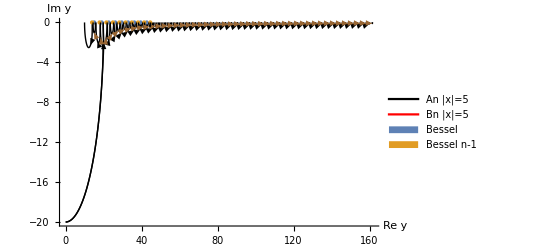

```mathematica
PlotTraj[{evoAx2c,evoBx2c},{"An |x|=5","Bn |x|=5"},{pointsRB2c,pointsRB3c},{"Bessel","Bessel n-1"},PlotRange->All,AxesOrigin-> Automatic,AxesLabel->{"Re y", "Im y"}]
```

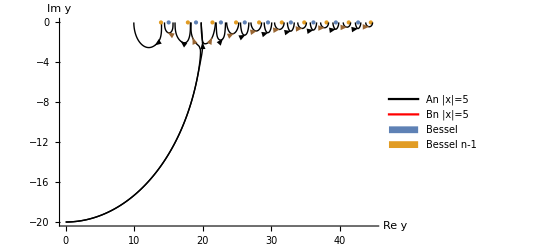

```mathematica
PlotTraj[{evoAx2c⟦1;;10⟧,evoBx2c⟦1;;10⟧},{"An |x|=5","Bn |x|=5"},{pointsRB2c,pointsRB3c},{"Bessel","Bessel n-1"},PlotRange->All,AxesOrigin-> Automatic,AxesLabel->{"Re y", "Im y"}]
```

```mathematica
evoAx3c⟦1;;9⟧//Dimensions
```

{9,315,3}

```mathematica
evoAx5=evoAx2⟦1;;10⟧;
evoBx5=evoBx2⟦1;;10⟧;
```

```mathematica
evoAxUlttest=MultipleEvolution2D[A1[n,xc,yc],{argy,y},evoAx5⟦1;;3⟧,argx,{x,20,25,1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

$Aborted